```mathematica
Exit
```

```mathematica
Get[Echo@FileNameJoin[{ParentDirectory[NotebookDirectory[]],"CoBarSLink.m"}]]
CoBarSLink`Private`clearLibraries[]
```

/Users/Henrik/github/CoBarsLink/CoBarSLink.m

```mathematica
dataPol=Association@Table[
k->CoBarSample["EdgeSpaceSamplingWeight",3,ConstantArray[1.,k],1000000,"QuotientSpace"->False]["InputData"]
,{k,{4,8,16,32,64,128,256}}];

dataPolQuot=Association@Table[
k->CoBarSample["EdgeQuotientSpaceSamplingWeight",3,ConstantArray[1.,k],1000000,"QuotientSpace"->True]["InputData"]
,{k,{4,8,16,32,64,128,256}}];


f=x↦x/Mean[x];
```

Compiling cSampleRandomVariables[3]...

Reading build settings from /Users/Henrik/github/CoBarsLink/LibraryResources/Source/BuildSettings.m

Compilation done. Time elapsed = 2.54671 s.

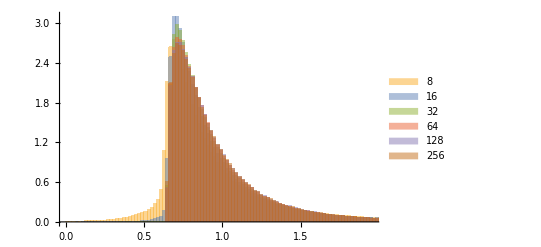

```mathematica
Histogram[f/@dataPolQuot[[2;;7]],10000,"PDF",ChartLegends->Automatic]
```

```mathematica
ListLinePlot[
Association[
"Var(norm. corr.)"->Transpose[{Keys[dataCorr],Variance/@(f/@Values[dataCorr])}],
"O(n^{-2})"->Transpose[{Keys[dataCorr],1/Keys[dataCorr]^2}]
],
ScalingFunctions->{"Log","Log"},
PlotMarkers->{Graphics[Disk[]], 10},
AxesLabel->{"edge count","variance"}
]
```

```mathematica
Histogram[{f@dataPol[[1]],f@dataPolQuot[[1]]},10000,"PDF",ChartLegends->Automatic]
```

```mathematica
Histogram[{f@dataPol[[3]],f@dataPolQuot[[3]]},10000,"PDF",ChartLegends->Automatic]
```

```mathematica
histPol=Histogram[f[#],10000,"PDF",PlotRange->{{0,2},All}]&/@dataPol;
```

```mathematica
histPolQuot=Histogram[f[#],10000,"PDF",PlotRange->{{0,2},All}]&/@dataPolQuot;
```

```mathematica
Column[Values@histPol]
```

```mathematica
Column[Values@histPolQuot]
```

```mathematica
"ChordLength"[1,Quotient[n,2]]
```

```mathematica
n=4 (*2 2 2*)
samplecount=10000000;

dataPol=CoBarSample["BendingEnergy",3,ConstantArray[1.,n],samplecount,"QuotientSpace"->False]

Correlation[dataPol["InputData"],dataPol["Weights"]]
```

```mathematica
test=WeightedData[dataPol["InputData"],dataPol["Weights"]];
dataPol==test
dataPol["InputData"]==test["InputData"]
dataPol["Weights"]==test["Weights"]
```

```mathematica
n=64;
X=Table[
y=RandomClosedPolygons[3,ConstantArray[1.,n],1]["ClosedPolygonUnitEdgeVectors"][[1]];
p=Total[RandomSample[y,10]];
Norm[p]
,{100000}];
```

```mathematica
Y=CoBarSample["ChordLength"[1,11],3,ConstantArray[1.,n],100000,"QuotientSpace"->True];
```

```mathematica
Histogram[{X,Y},"Wand","PDF"]
```

```mathematica
Histogram[Y]
```

```mathematica
n=4 (*2 2 2*)
samplecount=1000000;

dataPol=CoBarSample["BendingEnergy",3,ConstantArray[1.,n],samplecount,"QuotientSpace"->False]

Correlation[dataPol["InputData"],dataPol["Weights"]]
```

```mathematica
data=WeightedData[dataPol["InputData"],ConstantArray[1./samplecount,samplecount]];
```

```mathematica
Squared
```

```mathematica
Histogram[{dataPol,data},100,"PDF"]
```

```mathematica
data=WeightedData[dataPol["InputData"],ConstantArray[1./samplecount,samplecount]];
ω=WeightedData[dataPol["Weights"],ConstantArray[1./samplecount,samplecount]];
```

```mathematica
dataPol["InputData"]
```

```mathematica
Histogram[dataPol["Weights"],1000,"PDF"]
```

```mathematica
Total@ConstantArray[1./n,n]
```

```mathematica
dataPol["InputData"]//Dimensions
```

```mathematica
Histogram[dataPol[[1]]["InputData"],1000,"PDF"]
```

```mathematica
dataPolQuot=CoBarSample["ChordLength"[1,3],3,ConstantArray[1.,n],1000000,"QuotientSpace"->True]
```